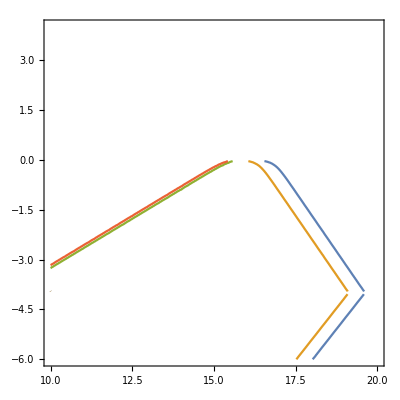

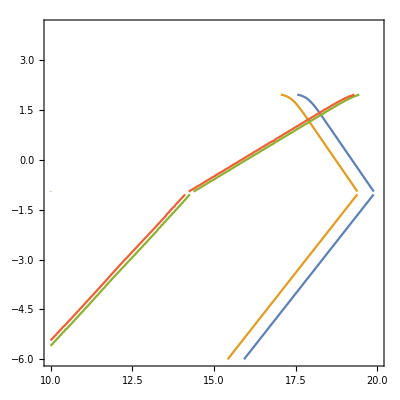

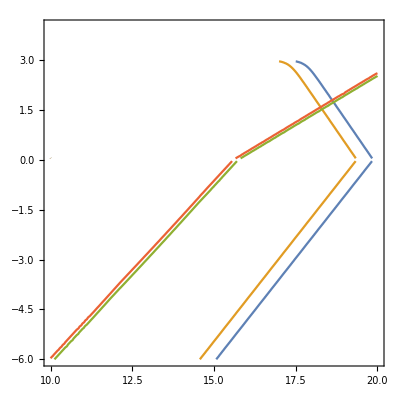

```mathematica
Clear["Global`*"];

(* Tbh in TeV and distance in cm, Flux in cm^-2 sec^-1 *)
Flux[dist_,Tbh_]:=1.4 10^29 Tbh^1.6/(4 Pi dist^2);

(* time to evaporation ie remaining lifetime in sec *)
TauEvap[Tbh_]:=407(1.06/Tbh)^3;

(* The first condition is to have at least X photons during the explosion; assuming that we start the observation a given time t0 to evaporation, we have that the longest observation time is that time t0*)

(* Note that a detector with a low and high energy threshold will only be sensitive to BH evaporation within that time-frame, corresponding to TauEvap of that threshold... *)

EffectiveTime[Tbh_,ELow_,EHigh_]:=If[Tbh>EHigh,10^-99,If[Tbh<ELow,TauEvap[ELow]-TauEvap[EHigh],TauEvap[Tbh]-TauEvap[EHigh]]];

(* Now let's see when a given detector can see 10 photons *)
(* let's use log10 scale for both Tbh and distance in cm *)

Aeff=0.8 10^4;

(*ContourPlot[Aeff*EffectiveTime[10^logtempBH,10^-4,1.]*Flux[10^logdis,10^logtempBH]==10.,{logdis,10,20},{logtempBH,-6,2}]*)

(* Now let's assume the background is: note energy in GeV here ...*)

GammaBack[ene_]:=1.4 10^(-6) ene^(-2.1);

(* Now let's assume that the average photon energy is... *)
AveragePhotonEnergy[Tbh_]:=10. Tbh^0.5;

(* and we want S/B=5 *)

(* Angular resolution of the LAT *)
deltaOmega=10^-3;
Aeff=0.8 10^4;
EL=0.1 10^-3;
EH=1.;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==10.},{logdis,10,20},{logtempBH,-6,4}]

(* Now for HAWC *)
deltaOmega=10^-5;
Aeff=5 10^4 10^4;
EL=0.1 ;
EH=10^2;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==10.},{logdis,10,20},{logtempBH,-6,4}]

(* Now for LHAASO *)
deltaOmega=10^-4;
Aeff=10^6 10^4;
EL=1. ;
EH=10^3;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==10.},{logdis,10,20},{logtempBH,-6,4}]
```

```mathematica
(* The calculations above are correct, but they have a serious flaw: the effective time does not account for the "Boltzmann tails"; let us now take that into account *)

(* Use the Ukawatta et al stuff for the spectrum; gamma-ray energy in GeV, BH mass in grams *)

x[egamma_,MBH_]:=egamma/(1058.(10^10/MBH));

(* parameterization in Eq. (31-34) of 1510.04372, all in GeV^-1 sec^-1 *)
Aparam=6.339 10^23;
Bparam=1.1367 10^24;
ThetaS[u_]:=0.5*(1.+Tanh[10.*u]);

d2NdEdtfrag[egamma_,MBH_]:=Aparam*x[egamma,MBH ]*(1-ThetaS[x[egamma,MBH ]-0.3])+Bparam*Exp[-x[egamma,MBH ]]*ThetaS[x[egamma,MBH ]-0.3]/(x[egamma,MBH ]*(x[egamma,MBH ]+1));

Ffunc[y_]:=If[y<2,1.,Exp[-0.0962-1.982(Log[y]-1.908)*(1.+Tanh[20.*(Log[y]-1.908)])]]


d2NdEdtdirect[egamma_,MBH_]:=(1.13 10^19 (x[egamma,MBH ])^6)/(Exp[x[egamma,MBH ]]-1.)*Ffunc[x[egamma,MBH ]]

(* Total differential flux from evaporation, in GeV^-1 sec^-1 *)
d2NdEdt[egamma_,MBH_]:=d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH];

(*MBHl=10^8;
LogLogPlot[{d2NdEdtfrag[eg,MBHl],d2NdEdtdirect[eg,MBHl]},{eg,10^-10,10^10}]*)

(*Elow=1. 10^-6;
Ehigh=10^10;
PhotonFlux[MBH_]:=NIntegrate[d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH],{egamma,Elow,Ehigh}];*)

(* CHeck that this is sensible *)
(*LogLogPlot[{PhotonFlux[MBHl],1.4 10^29 (1.058(10^10/MBHl))^1.6},{MBHl,10^2,10^16}]*)

(*Import effective areas: all in cm^2, with energies in GeV *)
SetDirectory[NotebookDirectory[]];
BATSE=Import["BATSE.dat","Table"];
GBM=Import["GBM.dat","Table"];
LAT=Import["LAT.dat","Table"];
HAWC=Import["HAWC.dat","Table"];
LHAASO=Import["LHAASO.dat","Table"];
VERITAS=Import["VERITAS.dat","Table"];

(* Energy in GeV, A_eff in cm^2 *)
(* GBM *)
ifun1=Interpolation[GBM,InterpolationOrder->1];
ELow1=150. 10^-6;
Ehigh1=40. 10^-3;
AeffGBM[ener_]:=If[ELow1<ener<Ehigh1,ifun1[ener],10.^-99];


(* BATSE *)
ifun2=Interpolation[BATSE,InterpolationOrder->1];
ELow2=30. 10^-6;
Ehigh2=10. 10^-3;
AeffBATSE[ener_]:=If[ELow2<ener<Ehigh2,ifun2[ener],10.^-99];

(* LAT *)
ifun3=Interpolation[LAT,InterpolationOrder->1];
ELow3=0.011258242220169287;
Ehigh3=3056.9907009353656;
AeffLAT[ener_]:=If[ELow3<ener<Ehigh3,ifun3[ener],10.^-99];


(* VERITAS *)
ifun4=Interpolation[VERITAS,InterpolationOrder->1];
ELow4=62.71501008536805;
Ehigh4=10000.;
AeffVERITAS[ener_]:=If[ELow4<ener<Ehigh4,ifun4[ener],10.^-99];

(* HAWC *)
ifun5=Interpolation[HAWC,InterpolationOrder->1];
ELow5=39.64823220312103;
Ehigh5=100000.;
AeffHAWC[ener_]:=If[ELow5<ener<Ehigh5,ifun5[ener],10.^-99];

(* LHAASO *)
ifun6=Interpolation[LHAASO,InterpolationOrder->1];
ELow6=20.423728794884738;
Ehigh6=2215412.2125811847;
AeffLHAASO[ener_]:=If[ELow6<ener<Ehigh6,ifun6[ener],10.^-99];

(* Check that everything works all right
LogLogPlot[{AeffLAT[y]},{y,10^-6,10^6}];
LogLogPlot[{AeffGBM[y],AeffBATSE[y],AeffLAT[y],AeffVERITAS[y],AeffHAWC[y],AeffLHAASO[y]},{y,10^-6,10^6}];
LogLogPlot[d2NdEdt[y,10^8],{y,0.5*ELow,1.5*Ehigh}];
NIntegrate[AeffGBM[y]*d2NdEdt[y,10^8],{y,10^-6,10^6}];
NIntegrate[AeffLHAASO[y]*d2NdEdt[y,10^8],{y,10^-6,10^6}];
*)

(* Now Load the background *)
BCKGdata=Import["EGB.dat","Table"];
ifun7=Interpolation[BCKGdata,InterpolationOrder->1];
EBCKG[zz_]:=Max[10.^-3*ifun7[zz]/zz^2,1.4 10^(-6) zz^(-2.1)];
(*LogLogPlot[{EBCKG[y],1.4 10^(-6) y^(-2.1)},{y,10^-6,10^6}]*)

(* Assume for now constant emission: let's calculate the signal to noise and total number of events *)
cminpc=3.086 10^18;
FluxAtDistance[egam_,MBHole_,distan_]:=d2NdEdt[egam,MBHole]/(4 Pi (distan cminpc)^2)




(* distance in pc *)
distance=1.;
MBH=10^8;


(*sig=NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,10.^8,1.],{y,10^-6,10^6}]
bckg=NIntegrate[AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]*)

(* Now let's integrate over time *)
(* Set the initial time-to-evaporation *)
tau=10^6;
BlackHoleMass[time_]:=10.^10(time/407.)^(1/3);

NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^4,10^6}]
```

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

16.4173

```mathematica
NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^-3,10^8}]
```

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

41.1376

```mathematica
NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^6],1.],{y,10^-6,10^6}]*10^6
```

4.19697

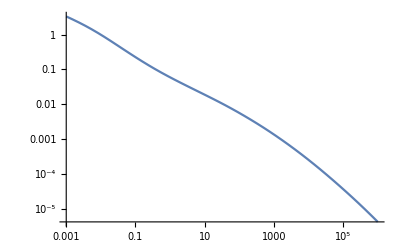

```mathematica
LogLogPlot[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^-3,10^6}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {954.672}. NIntegrate obtained 3.40721×10^7 and 117.821 for the integral and error estimates.

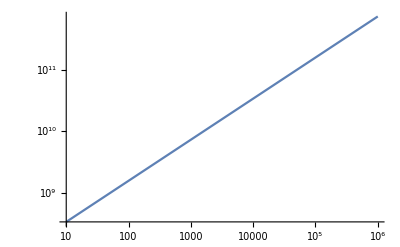

```mathematica
(*LogLogPlot[time*NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^1,10^6}]*)
```

```mathematica
(* It looks like the integral over time is roughly T*integrand ie. dominated at early times *)

(* Now for LHAASO *)
deltaOmega=10^-4;

ContourPlot[
NIntegrate[deltaOmega*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtime],10^logdis],{y,10^-6,10^6}]==10.,{logdis,-3,3},{logtime,2,8}]

ContourPlot[
(NIntegrate[deltaOmega*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtime],10^logdis],{y,10^-6,10^6}]/Sqrt[NIntegrate[deltaOmega*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]])==5.,{logdis,-3,3},{logtime,2,8}]
```

NIntegrate::inumr: The integrand 8.356×10^-43 10^(-2 «29») If[20.4237<y<«22»,«1»,1/(«1»)] ((4.8638×10^-65 10^(2 Charting`Private`pvar$1223912) y^6 If[1.27541×10^-14 Power[«2»]^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(1.27541×10^-14 Power[«2»] y))+(4.45622×10^37 ⅇ^(-«23» «1» y) (1.+Tanh[10. (-0.3+Times[«3»])]))/((10^(«29»))^(1/3) y (1+1.27541×10^-14 Power[«2»]^(1/3) y))+8.08482×10^9 (10^(Charting`Private`pvar$1223912))^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {143.357}. NIntegrate obtained 1.57797×10^9 and 1940.52 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3237.85}. NIntegrate obtained 0.000183548 and 1.42548×10^-8 for the integral and error estimates.

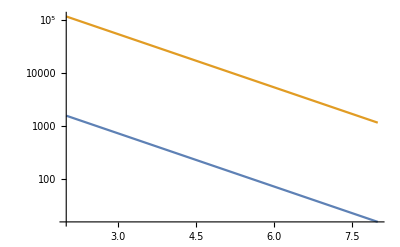

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {945.324}. NIntegrate obtained 3407.48 and 0.00740882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3237.85}. NIntegrate obtained 0.000183548 and 1.42548×10^-8 for the integral and error estimates.

251512.

```mathematica
(* Now for LHAASO *)
deltaOmegaLHAASO=10^-4;
deltaOmegaLAT=10^-3;
deltaOmegaHAWC=10^-5;
deltaOmegaVERITAS=10^-5;
deltaOmegaGBM=10^-3;

logtimez=1.;
logdisz=0.;

(*LogPlot[{NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtime],10^logdisz],{y,10^-6,10^6}],(NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtime],10^logdisz],{y,10^-6,10^6}]/Sqrt[NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]])},{logtime,2,8}]

(NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]])*)
```

```mathematica
logtimez=9.;
logdisz=0.;


(* Now for LHAASO *)
deltaOmegaLHAASO=10^-4;
deltaOmegaLAT=10^-3;
deltaOmegaHAWC=10^-5;
deltaOmegaVERITAS=10^-5;
deltaOmegaGBM=10^-3;
deltaOmegaBATSE=10^-3;

Print["LHAASO: ",
NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz]*10^logtimez,{y,10^-6,10^6}]];
Print["LHAASO S/N: ",10^logtimez*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]]];

Print["HAWC: ",
10^logtimez*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]];
Print["HAWC S/N: ",10^logtimez*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*EBCKG[y],{y,10^-6,10^6}]]];

Print["VERITAS: ",
10^logtimez*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]];
Print["VERITAS S/N: ",10^logtimez*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*EBCKG[y],{y,10^-6,10^6}]]];

Print["LAT: ",
10^logtimez*NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]];
Print["LAT S/N: ",10^logtimez*NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaLAT*AeffLAT[y]*EBCKG[y],{y,10^-6,10^6}]]];

Print["BATSE: ",
10^logtimez*NIntegrate[deltaOmegaBATSE*AeffBATSE[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}]];
Print["BATSE S/N: ",10^logtimez*NIntegrate[deltaOmegaBATSE*AeffBATSE[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaBATSE*AeffBATSE[y]*EBCKG[y],{y,10^-6,10^6}]]];

Print["GBM: ",
10^logtimez*NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}]];
Print["GBM S/N: ",10^logtimez*NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}]/Sqrt[10^logtimez*NIntegrate[deltaOmegaGBM*AeffGBM[y]*EBCKG[y],{y,10^-6,10^6}]]];
```

LHAASO: 7.34159×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3237.85}. NIntegrate obtained 0.000183548 and 1.42548×10^-8 for the integral and error estimates.

LHAASO S/N: 1.71362×10^7

HAWC: 5.32011×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1364.48883070936193462330265901982784271240234375}. NIntegrate obtained 3.75006×10^-6 and 2.70863×10^-10 for the integral and error estimates.

HAWC S/N: 868763.

VERITAS: 8.92285×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {10107.7}. NIntegrate obtained 0.0000459448 and 1.5801×10^-8 for the integral and error estimates.

VERITAS S/N: 416280.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.132617}. NIntegrate obtained 0.000180376 and 1.45605×10^-8 for the integral and error estimates.

LAT: 180376.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.132617}. NIntegrate obtained 0.000180376 and 1.45605×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.011263648134573053566538647363159952874411828815937042236328125}. NIntegrate obtained 0.000328515 and 2.46076×10^-9 for the integral and error estimates.

LAT S/N: 314.704

BATSE: 8975.84

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0000300023}. NIntegrate obtained 1.48523 and 0.000138614 for the integral and error estimates.

BATSE S/N: 0.232905

GBM: 1928.48

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.000150077}. NIntegrate obtained 0.0122836 and 2.15961×10^-6 for the integral and error estimates.

GBM S/N: 0.55024

```mathematica
(* Now compute the curves *)

fileout = OpenWrite["constraintdef.dat",FormatType->OutputForm];

Do[
logtimez=0.0+i*0.5;
LHAASON=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}];
LHAASOSN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]];

LHAASONc=Sqrt[LHAASON/10.];
LHAASOSNc=Sqrt[LHAASOSN/5.];
LHAASOconst=Min[LHAASONc,LHAASOSNc];



HAWCN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}];
HAWCSN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*EBCKG[y],{y,10^-6,10^6}]];

HAWCNc=Sqrt[HAWCN/10.];
HAWCSNc=Sqrt[HAWCSN/5.];
HAWCconst=Min[HAWCNc,HAWCSNc];

LATN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}];
LATSN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLAT*AeffLAT[y]*EBCKG[y],{y,10^-6,10^6}]];

LATNc=Sqrt[LATN/10.];
LATSNc=Sqrt[LATSN/5.];
LATconst=Min[LATNc,LATSNc];

VERITASN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}];
VERITASSN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[10^logtimez],10^logdisz],{y,10^-6,10^6}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*EBCKG[y],{y,10^-6,10^6}]];

VERITASNc=Sqrt[VERITASN/10.];
VERITASSNc=Sqrt[VERITASSN/5.];
VERITASconst=Min[VERITASNc,VERITASSNc];

GBMN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}];
GBMSN=Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[10^logtimez]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaGBM*AeffGBM[y]*EBCKG[y],{y,10^-6,10^6}]];

GBMNc=Sqrt[GBMN/10.];
GBMSNc=Sqrt[GBMSN/5.];
GBMconst=Min[GBMNc,GBMSNc];

Print[BlackHoleMass[10^logtimez]," ",10^logtimez," ",LHAASOconst," ",HAWCconst," ",LATconst," ",VERITASconst," ",GBMconst];
WriteString[fileout,CForm[10^logtimez],"  ",CForm[BlackHoleMass[10^logtimez]],"  ",CForm[LHAASOconst],"  ",CForm[HAWCconst],"  ",CForm[LATconst],"  ",CForm[VERITASconst],"  ",CForm[GBMconst]];
WriteString[fileout,"\n"];
,{i,0,40}];

Close[fileout];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3237.85}. NIntegrate obtained 0.000183548 and 1.42548×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1364.48883070936193462330265901982784271240234375}. NIntegrate obtained 3.75006×10^-6 and 2.70863×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.011263648134573053566538647363159952874411828815937042236328125}. NIntegrate obtained 0.000328515 and 2.46076×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.34938×10^9 1. 0.000770662 0.000147852 3.86972×10^-6 0.000245682 1.38871×10^-7

1.98062×10^9 3.16228 0.00102368 0.000195766 7.36453×10^-6 0.000363295 2.03835×10^-7

2.90716×10^9 10. 0.00137127 0.000253722 0.000012478 0.000521039 2.99191×10^-7

4.26712×10^9 31.6228 0.00182388 0.000320738 0.0000198483 0.000735004 4.39157×10^-7

6.26328×10^9 100. 0.00237166 0.000393665 0.0000303921 0.00102625 6.44602×10^-7

9.19324×10^9 316.228 0.00300039 0.000467796 0.0000454786 0.00141831 9.46165×10^-7

1.34938×10^10 1000. 0.00368247 0.000536601 0.0000672161 0.0019233 1.04913×10^-6

1.98062×10^10 3162.28 0.0043758 0.000594447 0.0000988301 0.00252867 1.15482×10^-6

2.90716×10^10 10000. 0.00503146 0.000637087 0.00014507 0.00315118 1.27118×10^-6

4.26712×10^10 31622.8 0.00510143 0.000665227 0.0001675 0.00366212 1.39931×10^-6

6.26328×10^10 100000. 0.0041351 0.000679522 0.000184009 0.0038449 1.54042×10^-6

9.19324×10^10 316228. 0.00325995 0.000677482 0.000201987 0.00295371 1.69586×10^-6

1.34938×10^11 1.×10^6 0.00248912 0.000657109 0.000221661 0.00215345 1.86716×10^-6

1.98062×10^11 3.16228×10^6 0.00184278 0.000464377 0.000243421 0.00152869 2.05604×10^-6

2.90716×10^11 1.×10^7 0.00132761 0.000308838 0.000267603 0.00111166 2.26449×10^-6

4.26712×10^11 3.16228×10^7 0.000924795 0.000199538 0.000290471 0.000804635 2.46218×10^-6

6.26328×10^11 1.×10^8 0.000472913 0.000096897 0.000239602 0.00039007 2.03509×10^-6

9.19324×10^11 3.16228×10^8 0.000227942 0.0000435419 0.000197809 0.000141476 1.68322×10^-6

1.34938×10^12 1.×10^9 0.000105015 0.0000184172 0.000163244 0.0000344037 1.39362×10^-6

1.98062×10^12 3.16228×10^9 0.0000473353 5.44273×10^-6 0.000134431 4.98372×10^-6 1.15569×10^-6

2.90716×10^12 1.×10^10 0.0000210062 9.18339×10^-7 0.0001104 3.28363×10^-7 9.60793×10^-7

4.26712×10^12 3.16228×10^10 5.97541×10^-6 7.11848×10^-8 0.000090212 6.3063×10^-9 8.02×10^-7

6.26328×10^12 1.×10^11 9.29361×10^-7 1.72206×10^-9 0.0000732002 9.19438×10^-12 6.73929×10^-7

9.19324×10^12 3.16228×10^11 6.10191×10^-8 7.13115×10^-12 0.0000589922 3.38099×10^-57 5.72704×10^-7

1.34938×10^13 1.×10^12 1.0975×10^-9 5.21724×10^-57 0.0000472217 2.78864×10^-57 4.96093×10^-7

1.98062×10^13 3.16228×10^12 5.14471×10^-57 4.30317×10^-57 0.0000374829 2.30006×10^-57 4.43951×10^-7

2.90716×10^13 1.×10^13 4.24334×10^-57 3.54924×10^-57 0.0000293805 1.89708×10^-57 4.19312×10^-7

4.26712×10^13 3.16228×10^13 3.49989×10^-57 2.9274×10^-57 0.0000226139 1.56471×10^-57 4.31479×10^-7

6.26328×10^13 1.×10^14 2.88669×10^-57 2.41451×10^-57 0.0000169506 1.29056×10^-57 5.03549×10^-7

9.19324×10^13 3.16228×10^14 2.38093×10^-57 1.99147×10^-57 0.000012241 1.06445×10^-57 6.47527×10^-7

1.34938×10^14 1.×10^15 1.96377×10^-57 1.64255×10^-57 8.42031×10^-6 8.7795×10^-58 7.30677×10^-7

1.98062×10^14 3.16228×10^15 1.61971×10^-57 1.35476×10^-57 5.46995×10^-6 7.24126×10^-58 7.01145×10^-7

2.90716×10^14 1.×10^16 1.33592×10^-57 1.1174×10^-57 3.36086×10^-6 5.97253×10^-58 6.20687×10^-7

4.26712×10^14 3.16228×10^16 1.10185×10^-57 9.21619×10^-58 1.95685×10^-6 4.85549×10^-58 5.25601×10^-7

6.26328×10^14 1.×10^17 9.08797×10^-58 7.49231×10^-58 1.08992×10^-6 4.00466×10^-58 4.34169×10^-7

9.19324×10^14 3.16228×10^17 7.49565×10^-58 6.17943×10^-58 5.90529×10^-7 3.30293×10^-58 3.55145×10^-7

1.34938×10^15 1.×10^18 6.0933×10^-58 5.0966×10^-58 3.18112×10^-7 2.72415×10^-58 2.90381×10^-7

1.98062×10^15 3.16228×10^18 5.02556×10^-58 4.20351×10^-58 1.69201×10^-7 2.24679×10^-58 2.38338×10^-7

2.90716×10^15 1.×10^19 4.1449×10^-58 3.46691×10^-58 8.3487×10^-8 1.85307×10^-58 1.96594×10^-7

4.26712×10^15 3.16228×10^19 3.41856×10^-58 2.85938×10^-58 3.61961×10^-8 1.52835×10^-58 1.62467×10^-7

6.26328×10^15 1.×10^20 2.81949×10^-58 2.3583×10^-58 1.28357×10^-8 1.26052×10^-58 1.33698×10^-7

```mathematica
(* I want to understand how big of a factor it is to integrate in time *)
NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,0.5*10^8,10^8}]
NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^5,10^8}]
NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^2,10^8}]
NIntegrate[NIntegrate[AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],1.],{y,10^-6,10^6}],{time,10^-1,10^8}]
```

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

2.04701

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

26.2083

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

39.9477

NIntegrate::inumr: The integrand 8.356×10^-39 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

41.0878

```mathematica
(* Now compute full-glory *)

fileout = OpenWrite["constraintfull.dat",FormatType->OutputForm];

Do[
logtimez=0.0+i*0.5;
LHAASON=NIntegrate[NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}];
LHAASOSN=NIntegrate[NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLHAASO*AeffLHAASO[y]*EBCKG[y],{y,10^-6,10^6}]];

LHAASONc=Sqrt[LHAASON/10.];
LHAASOSNc=Sqrt[LHAASOSN/5.];
LHAASOconst=Min[LHAASONc,LHAASOSNc];



HAWCN=NIntegrate[NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}];
HAWCSN=NIntegrate[NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaHAWC*AeffHAWC[y]*EBCKG[y],{y,10^-6,10^6}]];

HAWCNc=Sqrt[HAWCN/10.];
HAWCSNc=Sqrt[HAWCSN/5.];
HAWCconst=Min[HAWCNc,HAWCSNc];

LATN=NIntegrate[NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}];
LATSN=NIntegrate[NIntegrate[deltaOmegaLAT*AeffLAT[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaLAT*AeffLAT[y]*EBCKG[y],{y,10^-6,10^6}]];

LATNc=Sqrt[LATN/10.];
LATSNc=Sqrt[LATSN/5.];
LATconst=Min[LATNc,LATSNc];

VERITASN=NIntegrate[NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}];
VERITASSN=NIntegrate[NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*FluxAtDistance[y,BlackHoleMass[time],10^logdisz],{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaVERITAS*AeffVERITAS[y]*EBCKG[y],{y,10^-6,10^6}]];

VERITASNc=Sqrt[VERITASN/10.];
VERITASSNc=Sqrt[VERITASSN/5.];
VERITASconst=Min[VERITASNc,VERITASSNc];

GBMN=NIntegrate[NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[time]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}];
GBMSN=NIntegrate[NIntegrate[deltaOmegaGBM*AeffGBM[y]*d2NdEdtfrag[y,BlackHoleMass[time]]/(4 Pi (10^logdisz cminpc)^2),{y,10^-6,10^6}],{time,Max[10^-1,10^logtimez-3 10^7],10^logtimez}]/Sqrt[Min[3 10^7,10^logtimez]*NIntegrate[deltaOmegaGBM*AeffGBM[y]*EBCKG[y],{y,10^-6,10^6}]];

GBMNc=Sqrt[GBMN/10.];
GBMSNc=Sqrt[GBMSN/5.];
GBMconst=Min[GBMNc,GBMSNc];

Print[BlackHoleMass[10^logtimez]," ",10^logtimez," ",LHAASOconst," ",HAWCconst," ",LATconst," ",VERITASconst," ",GBMconst];
WriteString[fileout,CForm[10^logtimez],"  ",CForm[BlackHoleMass[10^logtimez]],"  ",CForm[LHAASOconst],"  ",CForm[HAWCconst],"  ",CForm[LATconst],"  ",CForm[VERITASconst],"  ",CForm[GBMconst]];
WriteString[fileout,"\n"];
,{i,0,40}];

Close[fileout];
```

NIntegrate::inumr: The integrand 8.356×10^-43 If[20.4237<y<2.21541×10^6,ifun6[y],1/10.^99] ((0.000048638 time^2 y^6 If[0.000127541 time^(1/3) y<2,1.,Exp[-0.0962-Times[«3»]]])/(-1.+ⅇ^(0.000127541 Power[«2»] y))+(4.45622×10^27 ⅇ^(-0.000127541 «1»«1»y) (1.+Tanh[10. (-0.3+Times[«3»])]))/(time^(1/3) y (1+0.000127541 time^(1/3) y))+8.08482×10^19 time^(1/3) y (1-0.5 (1.+Tanh[Times[«2»]]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000000,1000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3237.85}. NIntegrate obtained 0.000183548 and 1.42548×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1364.48883070936193462330265901982784271240234375}. NIntegrate obtained 3.75006×10^-6 and 2.70863×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.011263648134573053566538647363159952874411828815937042236328125}. NIntegrate obtained 0.000328515 and 2.46076×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.34938×10^9 1. 0.000925698 0.000170162 3.29541×10^-6 0.000255672 1.5065×10^-7

1.98062×10^9 3.16228 0.00133229 0.000250684 6.84564×10^-6 0.000414032 2.36834×10^-7

2.90716×10^9 10. 0.0018477 0.000347679 0.0000126141 0.000628445 3.57826×10^-7

4.26712×10^9 31.6228 0.00251803 0.000464621 0.0000213756 0.000919495 5.32025×10^-7